# Visualization of Logs

## Import Logs

```mathematica
FileAddress="C:\\Users\\MJavad\\Dropbox\\PSH-MJ\\log.txt";
Data = Import[FileAddress,"Data"];
(*Data=Data[[1;;405,All]];*)
lenData=Length[Data[[All,1]]];

readArray = Function[len,
i+=len;
Data[[All,i-len;;i-1]]
];

read = Function[,
readArray[1][[All,1]]
];

read2DArray = Function[{i,j},
Table[readArray[j],{n,1,i}]ᵀ
];

i = 1;
timeStart=read[];
timeEnd=read[];
PHD3to0 = readArray[3];
PLH1to0 = readArray[3];
PLH5to0 = readArray[3];
PLH6to0 = readArray[3];
PRH1to0 = readArray[3];
PRH5to0 = readArray[3];
PRH6to0 = readArray[3];
PLL1to0 = readArray[3];
PLL4to0 = readArray[3];
PLL6to0 = readArray[3];
PLL7to0 = readArray[3];
PRL1to0 = readArray[3];
PRL4to0 = readArray[3];
PRL6to0 = readArray[3];
PRL7to0 = readArray[3];
com = readArray[3];
comHD =readArray[3];
comLH =readArray[3];
comRH =readArray[3];
comLL =readArray[3];
comRL =readArray[3];
saLL=read2DArray[10,3];
saRL=read2DArray[10,3];
ang=readArray[2];
(*sa=read2DArray[12,3];*)
saCenter=readArray[3];
comR=readArray[3];
error=read[];
errorFilter=read[];
ankleSensor=read[];
ankleCommand=read[];
ankleTarget=read[];
```

## Plot

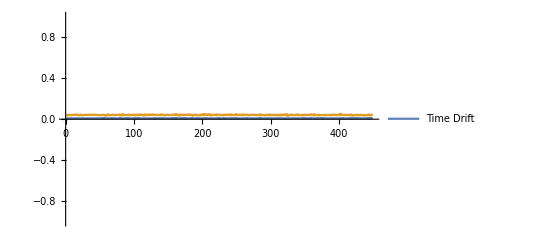

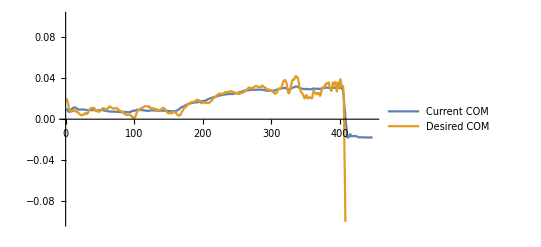

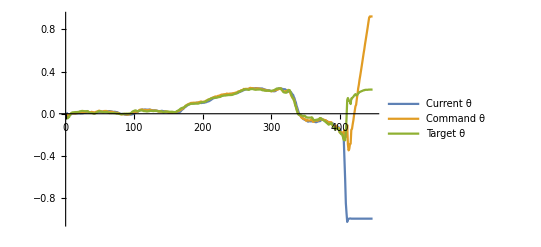

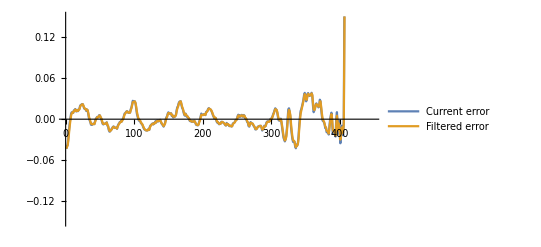

```mathematica
Rx[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}});
Ry[θ_]:=({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}});

toR= Function[p,
p.Q0toRᵀ+P0toR
];

AtoR=Function[A,
Table[p.Q0toRᵀ+P0toR,{p,A}]
];

Drift=Function[A,
Table[A[[i]]-timeStart[[1]]-(i-1)/20,{i,1,lenData}]
];

ListStepPlot[{Drift[timeStart],Drift[timeEnd]},PlotRange->{-1,1},PlotLegends->{"Time Drift"}]
(*ListLinePlot[{ang[[All,2]]},PlotRange->{-0.15,0.15},PlotLegends->{"Gravity θ"}]*)
ListLinePlot[{comR[[All,1]],saCenter[[All,1]]},PlotRange->{-0.1,0.1},PlotLegends->{"Current COM","Desired COM"}]
ListLinePlot[{ankleSensor,ankleCommand,ankleTarget},PlotRange->All,PlotLegends->{"Current θ","Command θ","Target θ"}]
ListLinePlot[{error,errorFilter},PlotRange->{-0.15,0.15},PlotLegends->{"Current error", "Filtered error"}]

Manipulate[

Q0toR=Ry[ang[[i,2]]].Rx[ang[[i,1]]];

z=0;
Do[If[(p.Q0toRᵀ)[[3]]<z,z=(p.Q0toRᵀ)[[3]]],{p,saLL[[i]]}];
Do[If[(p.Q0toRᵀ)[[3]]<z,z=(p.Q0toRᵀ)[[3]]],{p,saRL[[i]]}];

P0toR={-saCenter[[i,1]],-saCenter[[i,2]],-z};

plot = Reap[

Sow[Graphics3D[{LightGreen,Polygon[{{0.2,0.2,-0.001},{-0.2,0.2,-0.001},{-0.2,-0.2,-0.001},{0.2,-0.2,-0.001}}]}]];

Sow[Graphics3D[{Thick,Line[AtoR[{{0,0,0},PHD3to0[[i]]}]]}]];

Sow[Graphics3D[{Thick,Line[AtoR[{{0,0,0},{0,0,0.100},PRH1to0[[i]],PRH5to0[[i]],PRH6to0[[i]]}]]}]];

Sow[Graphics3D[{Thick,Line[AtoR[{{0,0,0},{0,0,0.100},PLH1to0[[i]],PLH5to0[[i]],PLH6to0[[i]]}]]}]];

Sow[Graphics3D[{Thick,Line[AtoR[{{0,0,0},PRL1to0[[i]],PRL4to0[[i]],PRL6to0[[i]],PRL7to0[[i]]}]]}]];

Sow[Graphics3D[{Thick,Line[AtoR[{{0,0,0},PLL1to0[[i]],PLL4to0[[i]],PLL6to0[[i]],PLL7to0[[i]]}]]}]];

Sow[Graphics3D[{Blue,Sphere[toR[com[[i]]]*{1,1,0},0.006]}]];
Sow[Graphics3D[{Orange,Sphere[toR[com[[i]]],0.005]}]];
Sow[Graphics3D[{Orange,Sphere[toR[comHD[[i]]],0.004]}]];

Sow[Graphics3D[{Orange,Sphere[toR[comRH[[i]]],0.004]}]];
Sow[Graphics3D[{Orange,Sphere[toR[comLH[[i]]],0.004]}]];

Sow[Graphics3D[{Orange,Sphere[toR[comRL[[i]]],0.004]}]];
Sow[Graphics3D[{Orange,Sphere[toR[comLL[[i]]],0.004]}]];

Sow[Graphics3D[{Orange,Polygon[AtoR[saLL[[i]]]]}]];
Sow[Graphics3D[{Orange,Polygon[AtoR[saRL[[i]]]]}]];

(*Sow[Graphics3D[{Cyan,Polygon[sa[[i]]]}]];*)
(*Sow[Graphics3D[{Cyan,Sphere[saCenter[[i]],0.006]}]];*)
Sow[Graphics3D[{Cyan,Sphere[{0,0,0},0.006]}]];

][[2,1]];


Show[plot,Boxed->False,Background->RGBColor[0.84,0.92,1]]

,{i,1,lenData,1}]
```